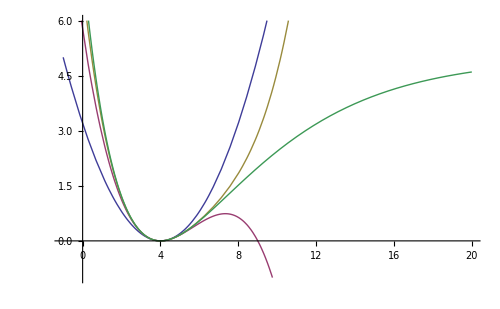

```mathematica
V=De(1-Exp[-a(r-re)])^2;
l={De->5,a->0.2,re->4};
Plot[{T2n/.l,T3n/.l,T4n/.l,V/.l},{r,-1,20},PlotRange->{-1,6},ImageSize->500]
```

```mathematica
T2=Series[V,{r,re,2}];
T2n=Normal[T2]
T3=Series[V,{r,re,3}];
T3n=Normal[T3]
T4=Series[V,{r,re,4}];
T4n=Normal[T4]
```

a^2 De (r-re)^2

a^2 De (r-re)^2-a^3 De (r-re)^3

a^2 De (r-re)^2-a^3 De (r-re)^3+7/12 a^4 De (r-re)^4